```mathematica
<<UNET`
```

## Training

```mathematica
hearts  = FileNames["*.tiff", "C:\\Users\\Matteo\\Desktop\\hearts", Infinity];
labels  = FileNames["*.tiff", "C:\\Users\\Matteo\\Desktop\\labels", Infinity];
rawData = {Import /@ hearts,Import /@ labels} //Transpose;
```

```mathematica
trainingData=Select[rawData,Length[#[[1]]]>1&];
selectLabels[item_]:=(Select[item//Transpose,ImageMeasurements[ColorConvert[#[[2]],"Grayscale"],"Mean"]!=0&]);
trainingData=ColorConvert[#,"Grayscale"]&/@Flatten[selectLabels/@trainingData];
trainingData=ImageResize[#,{96,96}, Resampling->"Nearest"]&/@trainingData;
trainingData=Partition[trainingData,2];
{data,label}=trainingData//Transpose;
data={ImageData[#]}&/@data;
label=Round[3*ImageData[#]+1]&/@label;
```

```mathematica
{train,valid,testData,testLabel,order}=SplitTrainData[data,label];
```

Dimensions data: {164,1,96,96} - Dimensions label: {164,96,96}

Number of Samples in each set: {115,33,16}

```mathematica
(*train the net*)
{{net,trained,netTrained},{result,iou}}=TrainUNET[train,valid,{testData,testLabel},BatchSize->16,MaxTrainingRounds->3000,NetParameters->32,TargetDevice->{"GPU", 1},LearningRate->.00002,
AugmentTrainData->{"90",True,True},BlockType->"ResNet"];
Export["netTrained2D.wlnet", netTrained];
```

channels: 1 - classes: 4 - Dimensions :{96,96}

Evaluating test data

DICE per class: {1→0.909,2→0.909,3→0.909,4→0.909}

## Graphics

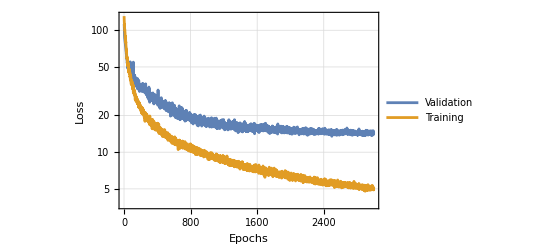
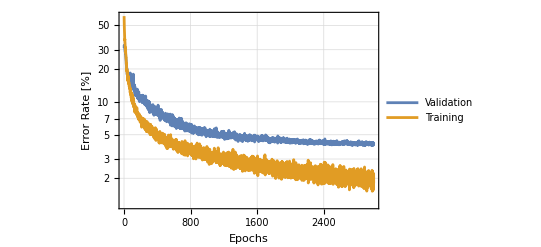

```mathematica
MakeNetPlots[trained]
```

```mathematica
Information[netTrained , "SummaryGraphic"]
```

-Graphics-

```mathematica
Show[%29,ImageSize->{1019,267},AspectRatio->Full]
```

-Graphics-

```mathematica
net
```

NetGraph[…]

```mathematica
netTrained = Import["C:\\Users\\Matteo\\Desktop\\repo\\uni\\cmr-segmentation\\src\\netTrained-nofilter.wlnet"]
VisualizeUNET2D[testData,netTrained]
```

NetGraph[<10>, <15>]

```mathematica
data //Dimensions
```

{164,1,128,128}

```mathematica
valid[[1, 1]] //Dimensions
```

{1,96,96}

```mathematica
Image /@ (netTrained /@ testData)[[;; , ;;, ;;, 2;;4]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageAdjust /@ Image /@ testLabel
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageAdjust /@ Image /@ testData[[;;, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SetDirectory []
```

C:\Users\Matteo

```mathematica
Export["Desktop\\netTrained-nofilter.wlnet", netTrained, "WLNet"];
netTrainedI =  Import["C:\\Users\\Matteo\\Desktop\\netTrained.wlnet"];
```